## bands

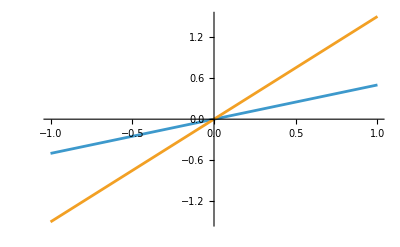

```mathematica
Plot[{x/2,3x/2},{x,-1,1}]
```

```mathematica
Clear[k,p,pl];
lim=3;x=1.75;
style={Directive[Darker[Red],Opacity[0.75],Specularity[5]],(**)Directive[Darker[Blue],Opacity[0.5],Specularity[5]]};

p=Plot3D[{1/2 √(ky^2+kx^2) x,(**)3/2 √(ky^2+kx^2),-1/2 √(ky^2+kx^2) x,-3/2 √(ky^2+kx^2) },{kx,-lim,lim},{ky,-lim,lim},PlotStyle->style,Lighting->"Neutral",Ticks->False,Mesh->None,PlotRange->{-12,12},PlotPoints->50,BaseStyle->{FontFamily->"TexMaths Symbols",24,Black,Bold},LabelStyle->Black,Axes->True,AxesLabel->{"k_x","k_y","E"},AxesOrigin->{0,0,0},Boxed->False,ImageSize->300,BoxRatios->{1,1,1.5},ViewPoint->{-2.2703309778058856,-2.4823352492084343,0.365525596575923},ImagePadding->{{20, 10}, {Automatic, 20}}];

hp1=Hyperplane[{0,0,4},{0,1,1.5}];
g=Graphics3D[{ {Opacity[0.3],Yellow,hp1},Boxed->False}];

txt=Text[Style[" μ",30,Bold,Darker[Brown],FontFamily->"TexMaths Symbols"]];im=Rasterize[txt,ImageResolution->300,Background->None];pl=Show[{p,g}, PlotRange->{{-lim, lim},{-lim,lim},Automatic},(**)Epilog->Inset[im,{0.1,0.575}],ImagePadding->{{20, 10}, {40,20}}(* {{left,right},{bottom,top}}*)]
SetDirectory[NotebookDirectory[]];
num=500;
Export["rsw.png",Rasterize[pl,ImageResolution->num,RasterSize->num,Background->None],ImageSize->num];
Clear[k];
```

-Graphics3D-

## Fermi surfaces

```mathematica
Plot[Sin[x],{x,0,10},Epilog->Inset[Graphics3D[Cylinder[],ImageSize->60,Boxed->False],{0.5,Center}]]
```

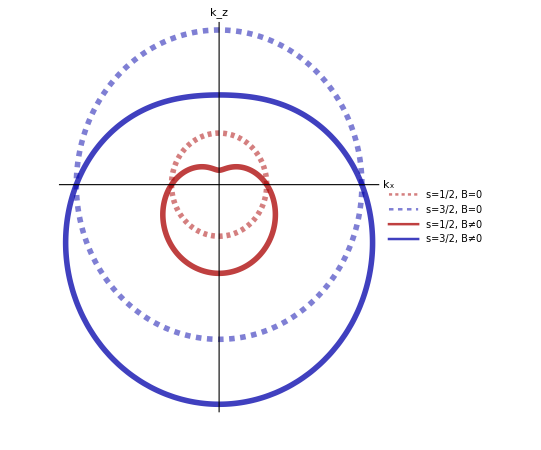

```mathematica
xc=-10;
rot=-π/2;lim=5;
thk=0.01;style={Directive[Darker[Red],Thickness[thk],Dashing[0.007],Opacity[0.5]],Directive[Darker[Blue],Thickness[thk],Dashing[0.01],Opacity[0.5]],(**)Directive[Darker[Red],Thickness[thk],Opacity[0.75]],Directive[Darker[Blue],Thickness[thk],Opacity[0.75]]};

txt=Text[Style["B",24,Bold,Black,FontFamily->"TexMaths Symbols"],{xc+0.05,-2}];
a={Arrowheads[{0.2}],Arrow[{{xc,-10},{xc,10}}]};
arr=Graphics[{{Darker[Green],Thickness[0.02],a}(*,txt*)},ImageSize->170];
rot=-π/2;μ=0.5;B=0.07;e=1;s=1/2;v0=1;st=3/2;
(***********)
pf=PolarPlot[{(*μ/(s v0),(μ+√(μ^2-2 B e s v0^2 Cos[θ+rot]))/(2 v0),μ/(st v0),(μ+√(μ^2-2 B e st v0^2 Cos[θ+rot]))/(2 v0)*)1,3,1-4 0.18Cos[θ+rot],3-7 0.18Cos[θ+rot]},{θ,0,2π},PlotPoints->50,AxesOrigin->{0,0},(*PlotRange->{{-5,3.5},Automatic},*)PlotStyle->style,Ticks->None,BaseStyle->{FontFamily->"TexMaths Symbols",24,Black,Bold},LabelStyle->Black,Axes->True,AxesLabel->{"k_x","k_z"},PlotLegends->Placed[LineLegend[{"s=1/2, B=0","s=3/2, B=0","s=1/2, B≠0","s=3/2, B≠0"},LabelStyle->{FontFamily->"TexMaths Symbols",18,Bold,Darker[Brown]},LegendLayout->"Row"],Below(*,{0.75,0.9}*)](**),Epilog->{Style[Text["B",{-4,2}],24,Bold,Darker[Green],FontFamily->"TexMaths Symbols"](**),Inset[arr,{-4,-0.15}]},ImageSize->400,ImagePadding->{{0,35}, {10, 40}}]
(*
SetDirectory[NotebookDirectory[]];
Export["rsw2.pdf",Rasterize[pf,RasterSize->650],ImageSize->650];*)
```

```mathematica
(* -Graphics- *)
(0.1/(3*6*10^(-4)/2))^2
(0.1/(6*10^(-4)/2))^2
```

12345.7

111111.